# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:=Exp[x+3]/(100 x+2)
```

b. Izračunajte definicijsko območje funkcije .
Df(f) = R∖{− 1/50}

```mathematica
FunctionDomain[f[x],x]
```

x<-1/50||x>-1/50

c. Izračunajte limite funkcije  na robovih definitives območja.

```mathematica
Limit[Exp[x+3]/(100 x+2),x->-1/50,Direction->-1]  (*leva limita*)
Limit[Exp[x+3]/(100 x+2),x->-1/50,Direction->1]   (*desna limita*)
Limit[Exp[x+3]/(100 x+2),x->Infinity]  (*x gre v+∞*)
Limit[Exp[x+3]/(100 x+2),x->-Infinity] (*x gre v-∞*)
```

∞

-∞

∞

0

d. Izračunajte odvod funkcije .

```mathematica
f[x_]:=Exp[x+3]/(100 x+2)
D[f[x],x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
(*Definiraj funkcijo*)f[x_]:=Exp[x+3]/(100 x+2)

(*Izračunaj prvo in drugo odvod funkcije*)
fPrime[x_]=D[f[x],x]
fPrime2[x_]=D[fPrime[x],x]

(*Poišči kritične točke (f'(x)=0)*)
kriticneTocke=Solve[fPrime[x]==0,x]

(*Preveri naravo ekstremov s pomočjo drugega odvoda*)
extremi=Table[{kriticneTocke[[i,1]],f[kriticneTocke[[i,1]]],fPrime2[kriticneTocke[[i,1]]]},{i,Length[kriticneTocke]}]

(*Izpiši rezultate*)
extremi
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

(20000 ⅇ^(3+x))/(2+100 x)^3-(200 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

{{x→49/50}}

{{x→49/50,ⅇ^(3+(x→49/50))/(2+100 (x→49/50)),(20000 ⅇ^(3+(x→49/50)))/(2+100 (x→49/50))^3-(200 ⅇ^(3+(x→49/50)))/(2+100 (x→49/50))^2+ⅇ^(3+(x→49/50))/(2+100 (x→49/50))}}

{{x→49/50,ⅇ^(3+(x→49/50))/(2+100 (x→49/50)),(20000 ⅇ^(3+(x→49/50)))/(2+100 (x→49/50))^3-(200 ⅇ^(3+(x→49/50)))/(2+100 (x→49/50))^2+ⅇ^(3+(x→49/50))/(2+100 (x→49/50))}}

D::ivar: 0.98 is not a valid variable.

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
(*Definiraj funkcijo*)f[x_]:=Exp[x+3]/(100 x+2)

(*Izračunaj prvi odvod funkcije*)
fPrime[x_]=D[f[x],x]

(*Poišči kritične točke (f'(x)=0)*)
kriticneTocke=Solve[fPrime[x]==0,x]

(*Preveri intervale,kjer je prvi odvod pozitiven ali negativen z uporabo Reduce*)
intervaliRast=Reduce[fPrime[x]>0,x]
intervaliPadanje=Reduce[fPrime[x]<0,x]

(*Izpiši intervale naraščanja in padanja*)
{intervaliRast,intervaliPadanje}
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

{{x→49/50}}

x>49/50

x<-1/50||-1/50<x<49/50

{x>49/50,x<-1/50||-1/50<x<49/50}

g. Narišite graf funkcije  na intervalu [-5, 5].

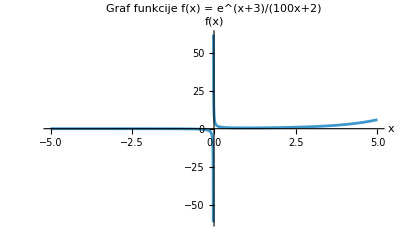

```mathematica
(*Definiraj funkcijo*)f[x_]:=Exp[x+3]/(100 x+2)

(*Nariši graf funkcije na intervalu[-5,5]*)
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","f(x)"},PlotLabel->"Graf funkcije f(x) = e^(x+3)/(100x+2)"]
```

h.

```mathematica
FunctionRange[{f[x],-Infinity<x<Infinity&&x!=-0.02},x,y]
```

y<0.||y≥0.53517

i. Izračunajte nedoločeni integral funkcije .

```mathematica
Integrate[f[x],x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
(*Izračunamo volumen vrtenine:V=π*∫[a,b] (f(x))^2 dx*)volume=N[Pi*Integrate[f[x]^2,{x,0.5,2}],3]
Print["Volumen vrtenine: ",volume]

(*Narišemo vrtenino*)
RevolutionPlot3D[f[x],{x,0.5,2},RevolutionAxis->"X",PlotLabel->"Vrtenina funkcije f(x) okoli x-osi",AxesLabel->{"x","y","z"}]
```

1.66479

Volumen vrtenine: 1.66479

-Graphics3D-

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
Clear[f[x_]]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
(*Definiramo funkcijo*)g[x_]:=(1+x^2.1)/(3+x)

(*Izračunamo vrednosti za x od 1 do 100*)
values=Table[g[x],{x,1,100}]

(*Izpišemo rezultat*)
Print["Vrednosti g(x) za x od 1 do 100: ",values]
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

Vrednosti g(x) za x od 1 do 100: {0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
(*Definiramo funkcijo*)g[x_]:=(1+x^2.1)/(3+x)

(*Izračunamo vrednosti za x od 1 do 100*)
values=Table[g[x],{x,1,100}];

(*Seznam praštevil na mestu enic:2,3,5,7*)
primes={2,3,5,7};

(*Izberemo vrednosti,kjer je cifra na mestu enic praštevilo*)
filteredValues=Select[values,MemberQ[primes,Mod[Floor[#],10]]&];

(*Izpišemo rezultat*)
Print["Vrednosti z enicami kot praštevilo: ",filteredValues]
```

Vrednosti z enicami kot praštevilo: {2.76845,3.79568,7.25393,12.3747,13.7134,15.0702,17.8313,22.0727,23.5093,27.8776,32.3228,33.8198,35.3238,42.9396,47.5778,52.2618,53.8326,55.4079,63.3483,73.005,77.8807,82.7856,87.7183,92.6772,95.9972,97.6613,102.669,107.7,112.754,117.828,122.923,133.171,143.492,145.219,152.146,153.883}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
(*Definiramo funkcijo g[x]*)g[x_]:=(1+x^2.1)/(3+x)

(*Izračunamo vrednosti za x od 1 do 100*)
values=Table[g[x],{x,1,100}];

(*Seznam praštevil na mestu enic*)
primes={2,3,5,7};

(*Izberemo vrednosti,kjer je cifra na mestu enic praštevilo*)
filteredValues=Select[values,MemberQ[primes,Mod[Floor[#],10]]&];

(*Definiramo anonimno funkcijo in jo uporabimo*)
result=Map[#^2+1&,filteredValues];

(*Izpišemo rezultat*)
Print["Rezultat po uporabi anonimne funkcije: ",result]
```

Rezultat po uporabi anonimne funkcije: {8.66433,15.4072,53.6195,154.134,189.057,228.11,318.954,488.203,553.686,778.158,1045.77,1144.78,1248.77,1844.81,2264.65,2732.29,2898.95,3071.03,4014.01,5330.73,6066.4,6854.46,7695.49,8590.07,9216.47,9538.73,10542.,11600.4,12714.4,13884.4,15111.,17735.4,20591.,21089.6,23149.5,23680.9}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
(*Definiramo funkcijo g[x]*)g[x_]:=(1+x^2.1)/(3+x)

(*Izračunamo vrednosti za x od 1 do 100*)
values=Table[g[x],{x,1,100}];

(*Seznam praštevil na mestu enic*)
primes={2,3,5,7};

(*Izberemo vrednosti,kjer je cifra na mestu enic praštevilo*)
filteredValues=Select[values,MemberQ[primes,Mod[Floor[#],10]]&];

(*Uporabimo anonimno funkcijo*)
result=Map[#^2+1&,filteredValues];

(*Zaokrožimo navzdol*)
flooredResult=Floor[result];

(*Izberemo števila,deljiva s 3,in jih seštejemo*)
divisibleBy3=Select[flooredResult,Mod[#,3]==0&];
sumDivisibleBy3=Total[divisibleBy3];

(*Izpišemo rezultat*)
Print["Števila, deljiva s 3: ",divisibleBy3];
Print["Vsota števil, deljivih s 3: ",sumDivisibleBy3]
```

Števila, deljiva s 3: {15,189,228,318,1248,2898,4014,6066,7695,9216,10542,12714,13884}

Vsota števil, deljivih s 3: 69027

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`